```mathematica
d[{x1_,y1_},{x2_,y2_}]:=(x2-x1)^2+(y2-y1)^2
```

```mathematica
draw[k_]:=Module[{},Print[Style[Graphics[{Table[Line[{{1/2,i+1/2},{n+1/2,i+1/2}}],{i,0,m}],Table[Line[{{i+1/2,1/2},{i+1/2,m+1/2}}],{i,0,n}],(Rectangle[#1-{1/2,1/2},#1+{1/2,1/2}]&)/@unused⟦k⟧,Text[Style["S",FontSize->20],{1,1-0.1}],Text[Style["F",FontSize->20],{n,m-0.1}]},AspectRatio->Automatic,PlotRange->{{1/2-.01,n+1/2+.01},{1/2-.01,m+1/2+.01}},ImageSize->20 {n,m}],Antialiasing->False]];Print[Style[Graphics[{Table[Line[{{1/2,i+1/2},{n+1/2,i+1/2}}],{i,0,m}],Table[Line[{{i+1/2,1/2},{i+1/2,m+1/2}}],{i,0,n}],(Rectangle[#1-{1/2,1/2},#1+{1/2,1/2}]&)/@unused⟦k⟧,AbsoluteThickness[3],Hue[0],Line[done⟦k⟧]},AspectRatio->Automatic,PlotRange->{{1/2-.01,n+1/2+.01},{1/2-.01,m+1/2+.01}},ImageSize->20 {n,m}],Antialiasing->False]]]
```

```mathematica
link[L_]:=Module[{dt,i},
If[Length[L]==1,Return[0]];
LL={0,0}~Join~L;
dt=L[[-1]]-L[[-2]];
i=1;
While[LL[[-i-1]]-LL[[-i-2]]==dt&&i<Length[L]-1,i++];
i]
```

```mathematica
prelink[L_]:=link[Drop[L,-link[L]]]
```

```mathematica
paths:=Module[{},
p={{{1,1}}};
done={};
While[Length[p]>0,
path=Last[p];
p=Reverse[Rest[Reverse[p]]];
pos=Last[path];
If[pos=={n,m}&&link[path]=!=prelink[path]&&Length[Complement[A,path]]≤z,
AppendTo[done,path],
touch=Select[A,d[#,pos]==1&&Not[MemberQ[path,#]]&]; pp=Map[path~Join~{#}&,touch];
ppp=Select[pp,link[#]>1||prelink[Drop[#,-1]]=!=link[Drop[#,-1]]||prelink[#]==0&];
p=p~Join~ppp]];
unused=Map[Complement[A,#]&,done];
unique=Select[Range[Length[done]],Count[unused,unused[[#]]]==1&];
unused=unused[[unique]];
done=done[[unique]];]
```

```mathematica
n=8;
m=5;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```

```mathematica
n=9;
m=5;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```

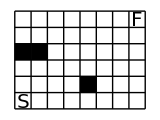

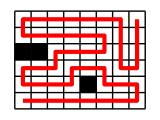

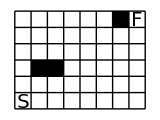

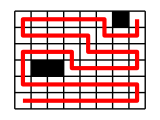

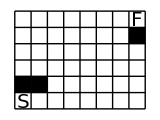

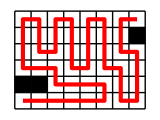

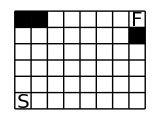

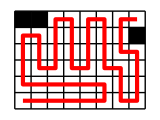

```mathematica
n=8;
m=6;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```

```mathematica
n=7;
m=7;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```

```mathematica
n=5;
m=10;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```

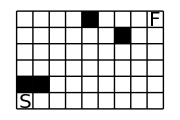

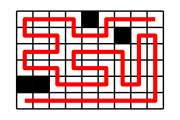

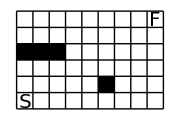

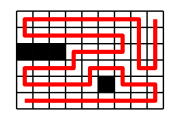

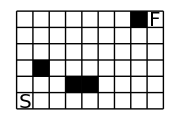

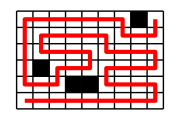

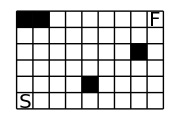

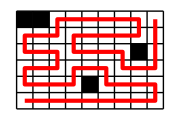

-Graphics-

-Graphics-

-Graphics-

«389 more identical outputs»

```mathematica
n=9;
m=6;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```

```mathematica
n=8;
m=7;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```

-Graphics-

-Graphics-

-Graphics-

«451 more identical outputs»

```mathematica
n=10;
m=6;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```

-Graphics-

-Graphics-

-Graphics-

«141 more identical outputs»

```mathematica
n=9;
m=7;
z=4;
A=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1];
paths;
For[k=1,k≤Length[done],k++,draw[k]]
```